## Problem 4 b

```mathematica
ngovern=Piecewise[{{1-t^(3/2), t≤ 1}, {0, t>1}}] ;
```

```mathematica
nexovern=Piecewise[{{t^(3/2), t≤ 1}, {1, t>1}}] ;
```

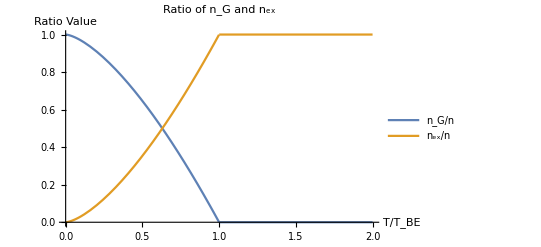

```mathematica
Plot[{ngovern,nexovern},{t,0,2},PlotLabel->"Ratio of n_G and n_ex",PlotLegends->{"n_G/n","n_ex/n"},Axes->True,AxesLabel->{T/Subscript[T, BE],Ratio Value}]
```